## Probability distributions of heat

```mathematica
(*First run dataCharFunCounting.nb *)

du = 0.5;
(*only positive values of u*)
uList = Table[char1[[j]][[1]],{j,1,Length[char1]}];
genList=Table[(char1[[j]][[2]]-1/2),{j,1,Length[char1]}];
NVals = Length[uList];
NegFreqPars=Reverse[Drop[genList ,1]];
AllFreqPars = Join[genList,Conjugate[NegFreqPars]];
PD=Fourier[AllFreqPars,FourierParameters->{1, -1}]/(2 NVals-1);
```

```mathematica
(*equivalent of function numpy.fft.fftfreq in Python*)
freq1={};
k = 0;
While[
k≤ NVals -1,
freq1 = Append[freq1,k/((2 NVals-1)du)];
k=k+1]
freq2={};
k = - NVals +1;
While[
k≤ -1,
freq2 = Append[freq2,k/((2 NVals-1)du)];
k=k+1]
```

```mathematica
heatVals=(2 Pi)Join[freq1,freq2];
```

```mathematica
heatValsShift = RotateRight[heatVals,NVals-1];
PDShift=RotateRight[PD,NVals-1];
```

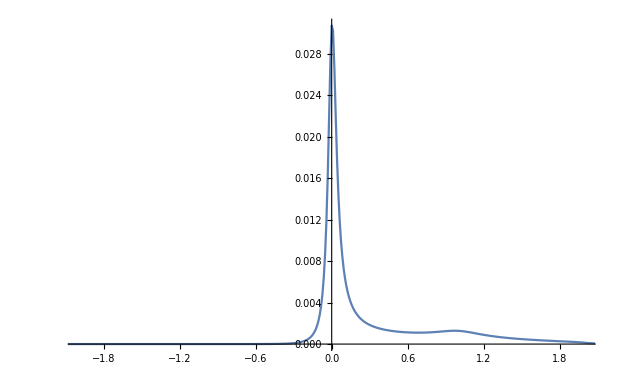

```mathematica
ListPlot[Transpose[{heatValsShift ,Abs[PDShift]}],Joined->True,PlotRange->{{-2,2},All}]
```